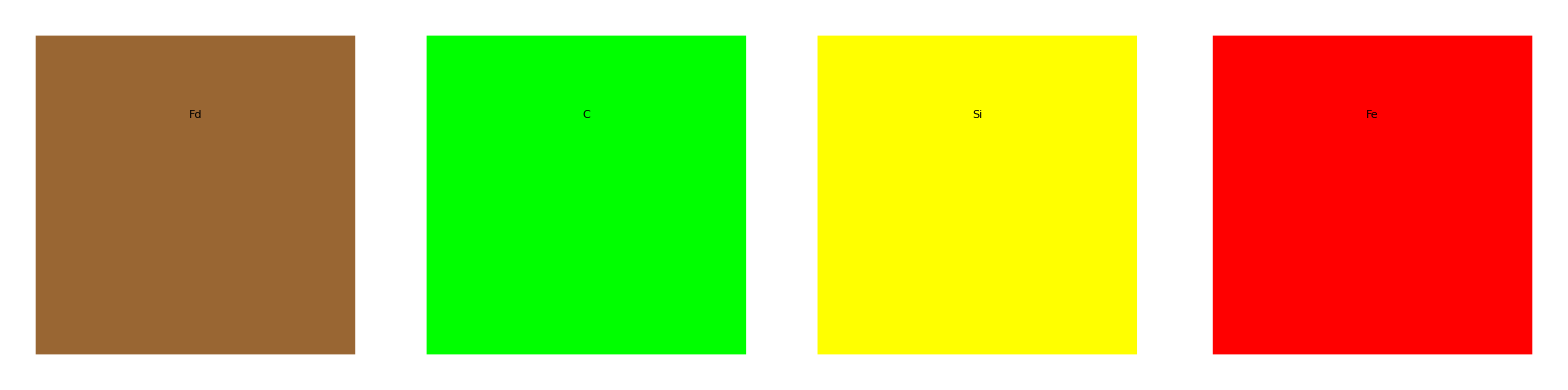

```mathematica
resources = {"Fd", "C", "Si", "Fe"};
colors = {Brown,Green,Yellow,Red};
gfx={0,0,0,0};
Do[
gfx⟦i⟧=Graphics[{colors⟦i⟧,Rectangle[],Black,Inset[Style[resources⟦i⟧,Large],{0.5,0.75}]},ImagePadding->None];
,{i,1,resources//Length}];
GraphicsRow[gfx,Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"resources.png",%135]
```

/home/charles/Dropbox/Games/TerraNova/sprites/resources.png

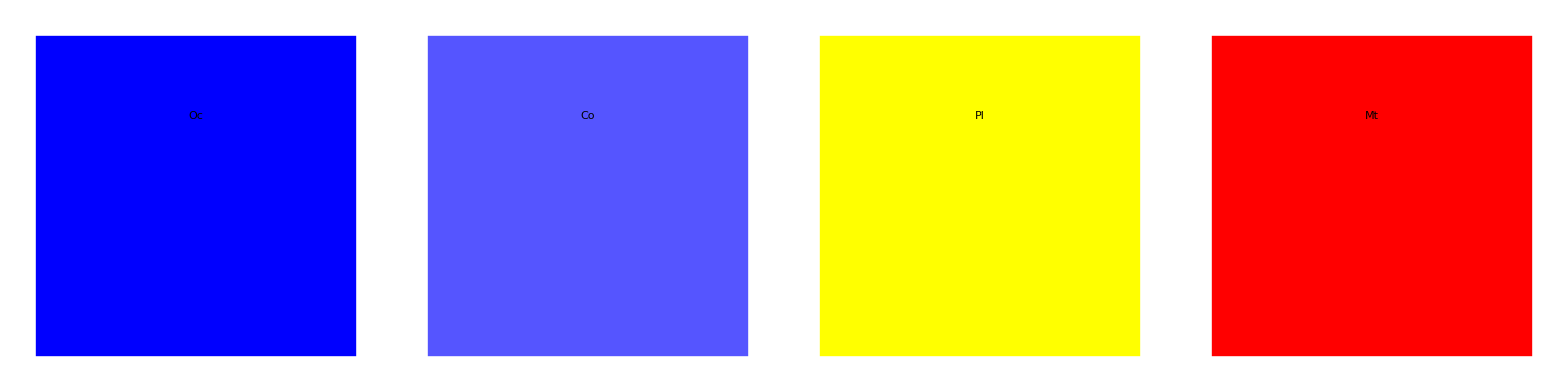

```mathematica
terrain = {"Oc","Co","Pl","Mt"};
terrainColors = {Blue,Lighter@Blue,Yellow,Red};
gfx={0,0,0,0};
Do[
gfx⟦i⟧=Graphics[{terrainColors⟦i⟧,Rectangle[],Black,Inset[Style[terrain⟦i⟧,Large],{0.5,0.75}]},ImagePadding->None];
,{i,1,terrain//Length}];
GraphicsRow[gfx,Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"terrain.png",%142]
```

/home/charles/Dropbox/Games/TerraNova/sprites/terrain.png

```mathematica
Graphics[{Black,Rectangle[],White,Inset[Style["C",Large]]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"colonist.png",%145]
```

/home/charles/Dropbox/Games/TerraNova/sprites/colonist.png